```mathematica
(*1. Ellenőrizzük a (2)-(5) egyenleteket. *)

(* 2 *)Simplify[Integrate[Sin[n*Pi*x/a]*Sin[m*Pi*x/a],{x,-a,a}],Element[{m,n},Integers]]
(* 2 *)Simplify[Integrate[Sin[n*Pi*x/a]*Sin[n*Pi*x/a],{x,-a,a}],Element[{n},Integers]]

(* 3 *)Simplify[Integrate[Sin[n*Pi*x/a]*Cos[m*Pi*x/a],{x,-a,a}],Element[{m,n},Integers]]
(* 3 *)(*Simplify[Integrate[Sin[n*Pi*x/a]*Cos[n*Pi*x/a],{x,-a,a}],Element[{n},Integers]]*)

(* 4 *)Simplify[Integrate[Sin[n*Pi*x/a],{x,-a,a}],Element[{n},Integers]]
(* 5 *)Simplify[Integrate[Cos[n*Pi*x/a],{x,-a,a}],Element[{n},Integers]]
```

0

a

0

0

0

«1 more identical outputs»

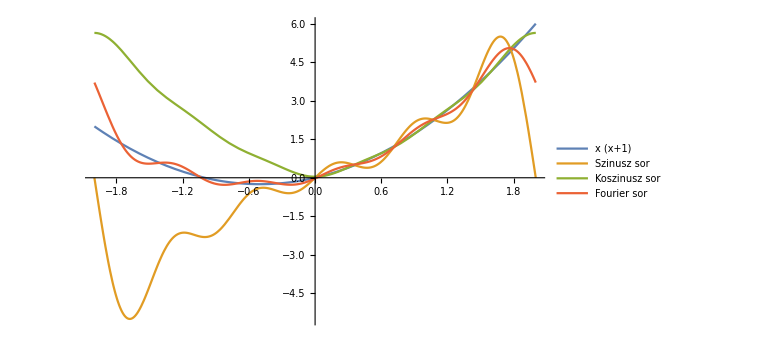

```mathematica
(*2.a. Írjuk meg a fourierSinCoefficient[f,x,m,a] függvényt,ami megadja azf(x)kifejezés(0,a)intervallumon vett szinusz soránakm-edik együtthatóját*)
fourierSinCoefficient[f_,x_,m_,a_] := 2/a* Integrate[f[x]*Sin[m*Pi*x/a], {x, 0, a}]
(* ..../; m == 0*)

(*2.a. Írjuk meg a fourierSinCoefficient[f,x,m,a] függvényt,ami megadja azf(x)kifejezés(0,a)intervallumon vett koszinusz soránakm-edik együtthatóját*)
(*fourierCosCoefficient[f_,x_,m_,a_] := 1/a*Integrate[f[x],{x, 0, a}]/;m==0
fourierCosCoefficient[f_,x_,m_,a_] := 2/a* Integrate[f[x]*Cos[m*Pi*x/a], {x, 0, a}]/;m≠0
*)
fourierCosCoefficient[f_,x_,m_,a_] :=If[m==0,1/a*Integrate[f[x],{x, 0, a}],2/a* Integrate[f[x]*Cos[m*Pi*x/a], {x, 0, a}]]



fourierTrigCoefficient[f_,x_,m_,a_,sc_]:=
If[sc==0,
If[m==0, 1/2/a*Integrate[f[x],{x,-a,a}],
1/a*Integrate[f[x]*Cos[m*Pi*x/a],{x,-a,a}]
],
1/a*Integrate[f[x]*Sin[m*Pi*x/a],{x,-a,a}]
];

(*2.c. *)
f[x_] = x(x+1);

fsin[f_,x_]=Sum[fourierSinCoefficient[f, x, n, 2]*Sin[n*Pi*x/2], {n, 0, 5}];
fcos[f_,x_]=Sum[fourierCosCoefficient[f, x, n, 2]*Cos[n*Pi*x/2], {n, 0, 5}];
ffourier[f_,x_]=Sum[fourierTrigCoefficient[f, x, n, 2, 0]*Cos[n*Pi*x/2]+fourierTrigCoefficient[f, x, n, 2, 1]*Sin[n*Pi*x/2], {n,0,5}];

(*ffourier[f,x]*)
(*fsin[f,x]*)
(*fcos[f,x]*)
(*Show[
Plot[f[x],{x,-2,2}],
Plot[ffourier[f,x],{x,-2,2}],
Plot[fsin[f,x],{x,-2,2}],
Plot[fcos[f,x],{x,-2,2}]
]*)

Plot[{
f[x],
fsin[f,x],
fcos[f,x],
ffourier[f,x]
}, {x, -2, 2},
PlotLegends->{f[x],"Szinusz sor", "Koszinusz sor","Fourier sor" },
ImageSize->Large
]
```

```mathematica
(*3. feladat *)
sol3=DSolveValue[
{D[u[t,x],t]==D[u[t,x],{x,2}],
u[0,x]==x*(1-x),
u[t,0]==0,
u[t,1]==0},u,{t,x}]/.{Infinity->10}//Activate;
plotSol3=Plot3D[sol3[t,x],{t,0,0.5},{x,0,1},
PlotRange->All,ImageSize->Medium,AxesLabel->{"t","x","u"},PlotStyle->{Red,Opacity[0.8]}];
```

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
g[x_]=x(1-x);
Bn[g_,x_,n_]=2/L*Integrate[g[x]*Sin[n*Pi*x/L],{x,0,L}];
u10[x_,t_]=Sum[Bn[g,x,n] * Sin[n*Pi*x/L]*Exp[-(n*Pi*c/L)^2*t],{n,1,10}];
Plotu10=Plot3D[u10[t,x],{t,0,0.5},{x,0,1},
PlotRange->All,ImageSize->Medium,AxesLabel->{"t","x","u"}];
Show[
Plotu10,
plotSol3
]
```

-Graphics3D-

```mathematica
(*4. Feladat *)
```